#### Define fields, metric, potential, parameters

```mathematica
nf=2;
f=Table[Symbol["f"<>ToString[i]][t],{i,nf}];
{x,y}=f;

df=Table[Symbol["f"<>ToString[i]]'[t],{i,nf}](*f[[#]]'[t]&/@Table[n,{n,1,nf}]*);
ddf=Table[Symbol["f"<>ToString[i]]''[t],{i,nf}];

G=({{g[y], 0}, {0, 1}});
Ginv=Inverse[G];

dfNorm2=Simplify[df.G.df];
dfNorm=Simplify@Sqrt[dfNorm2];
sig=df/dfNorm;
K=1/2 dfNorm2;

gTest[y_]:=Exp[2 y/r0];
WTest[x_,y_]:=A Exp[x/r1](Tanh[x/r2]+1);
VTest[x_,y_]:=3 W[x,y]^2 - 2 Grad[W[x,y],f].Ginv.Grad[W[x,y],f](*+a^2/2(y-y0val)^2*)
```

```mathematica
VTest[x,y]//.W->WTest
```

3 A^2 ⅇ^((2 f1[t])/r1) (1+Tanh[f1[t]/r2])^2-(2 ((A ⅇ^(f1[t]/r1) Sech[f1[t]/r2]^2)/r2+(A ⅇ^(f1[t]/r1) (1+Tanh[f1[t]/r2]))/r1)^2)/g[f2[t]]

```mathematica
Vgrad=Grad[V[x,y],f];
VgradUp=Ginv.Vgrad;
Vhess=D[V[x,y],{f,2}];
Vsig=sig.Vgrad;

H=Sqrt[(K+V[x,y])/3];
eH=K/H^2;
```

```mathematica
Vgrad//.{V->VTest,W->WTest}
```

{6 A ⅇ^(f1[t]/r1) (1+Tanh[f1[t]/r2]) ((A ⅇ^(f1[t]/r1) Sech[f1[t]/r2]^2)/r2+(A ⅇ^(f1[t]/r1) (1+Tanh[f1[t]/r2]))/r1),0}

```mathematica
Grad[VTest[x,y],f]//.W->WTest
```

{6 A ⅇ^(f1[t]/r1) (1+Tanh[f1[t]/r2]) ((A ⅇ^(f1[t]/r1) Sech[f1[t]/r2]^2)/r2+(A ⅇ^(f1[t]/r1) (1+Tanh[f1[t]/r2]))/r1)-(4 ((2 A ⅇ^(f1[t]/r1) Sech[f1[t]/r2]^2)/(r1 r2)-(2 A ⅇ^(f1[t]/r1) Sech[f1[t]/r2]^2 Tanh[f1[t]/r2])/r2^2+(A ⅇ^(f1[t]/r1) (1+Tanh[f1[t]/r2]))/r1^2) ((A ⅇ^(f1[t]/r1) Sech[f1[t]/r2]^2)/r2+(A ⅇ^(f1[t]/r1) (1+Tanh[f1[t]/r2]))/r1))/g[f2[t]],(2 ((A ⅇ^(f1[t]/r1) Sech[f1[t]/r2]^2)/r2+(A ⅇ^(f1[t]/r1) (1+Tanh[f1[t]/r2]))/r1)^2 g'[f2[t]])/g[f2[t]]^2}

```mathematica
VgradUp[x,y]//.{g->gTest,V->VTest,W->WTest}
```

{6 A ⅇ^(f1[t]/r1-(2 f2[t])/r0) (1+Tanh[f1[t]/r2]) ((A ⅇ^(f1[t]/r1) Sech[f1[t]/r2]^2)/r2+(A ⅇ^(f1[t]/r1) (1+Tanh[f1[t]/r2]))/r1),0}[f1[t],f2[t]]

#### Geometric objects and mass matrix

```mathematica
csymb:=Simplify@Table[1/2 Sum[Ginv[[i,m]](D[G[[m,k]],f[[j]]]+D[G[[j,m]],f[[k]]]-D[G[[j,k]],f[[m]]]),{m,nf}],{i,nf},{j,nf},{k,nf}];
riemann:=Simplify@Table[D[csymb[[i,j,k]],f[[l]]]-D[csymb[[i,j,l]],f[[k]]]+Sum[csymb[[m,j,k]]csymb[[i,l,m]],{m,nf}]-Sum[csymb[[m,j,l]]csymb[[i,k,m]],{m,nf}],{i,nf},{j,nf},{l,nf},{k,nf}];
ricciT:=Table[Sum[riemann[[i,j,i,k]],{i,nf}],{j,nf},{k,nf}];
ricciS:=Sum[(Ginv.ricciT)[[i,i]],{i,nf}];
```

```mathematica
csymb//.g->gTest//MatrixForm
ricciS//.g->gTest
```

((0
1/r0) | (1/r0
0)
(-ⅇ^((2 f2[t])/r0)/r0
0) | (0
0))

-2/r0^2

```mathematica
Ddf=ddf+Table[Sum[csymb[[i,j,k]]df[[j]]df[[k]],{j,nf},{k,nf}],{i,nf}];
wVec=D[sig,t]+Table[Sum[csymb[[i,j,k]]df[[j]]sig[[k]],{j,nf},{k,nf}],{i,nf}];
w2=wVec.G.wVec;
w=Simplify@Sqrt[w2];
s=Simplify[wVec/w];
```

```mathematica
DdV=Vhess-Table[Sum[csymb[[i,j,k]]Vgrad[[i]],{i,nf}],{j,nf},{k,nf}];
massMx=Ginv.DdV-Table[Sum[riemann[[i,l,m,j]]df[[l]]df[[m]],{l,nf},{m,nf}],{i,nf},{j,nf}];
mSigSig=sig.G.massMx.sig;
mss=s.G.massMx.s;
```

```mathematica
eom=Ddf+3H df+VgradUp;
eomTest =Simplify[ eom//.{g->gTest,V->VTest,W->WTest}];
```

```mathematica
eomTest//MatrixForm
```

((6 A^2 ⅇ^((2 f1[t])/r1-(2 f2[t])/r0) (1+Tanh[f1[t]/r2]) (r2+r1 Sech[f1[t]/r2]^2+r2 Tanh[f1[t]/r2]))/(r1 r2)+(2 f1'[t] f2'[t])/r0+√(3/2) f1'[t] √(6 A^2 ⅇ^((2 f1[t])/r1) (1+Tanh[f1[t]/r2])^2-(4 A^2 ⅇ^((2 f1[t])/r1-(2 f2[t])/r0) (r2+r1 Sech[f1[t]/r2]^2+r2 Tanh[f1[t]/r2])^2)/(r1^2 r2^2)+ⅇ^((2 f2[t])/r0) f1'[t]^2+f2'[t]^2)+f1''[t]
(-2 ⅇ^((2 f2[t])/r0) f1'[t]^2+√6 r0 f2'[t] √(6 A^2 ⅇ^((2 f1[t])/r1) (1+Tanh[f1[t]/r2])^2-(4 A^2 ⅇ^((2 f1[t])/r1-(2 f2[t])/r0) (r2+r1 Sech[f1[t]/r2]^2+r2 Tanh[f1[t]/r2])^2)/(r1^2 r2^2)+ⅇ^((2 f2[t])/r0) f1'[t]^2+f2'[t]^2)+2 r0 f2''[t])/(2 r0))

#### Solve background equations of motion

```mathematica
tEnd=1*^3;
eHAsym=15*^-4;(*Asymptotic value of e_H where tanh has no effect, previously 25*)
wHAsym=484*^-2;(*previously 5, 25*)
r0val=Sqrt[2 eHAsym/wHAsym^2](*4*^-2*);
y0val=3r0val(*1*^-1*);
r1val=Sqrt[2 Exp[-2y0val/r0val]/eHAsym](*1/2*);
r2val=5*^-2;
N[r0val]
N[y0val]
N[r1val]
N[r2val]
Aval=1(*10^(-5)*);
aval=1*10^-3;
x0val=1;
yp0v=(*1*^-3*)0;
```

0.0113166

0.0339497

1.81797

0.05

```mathematica
Plot3D[VTest[x,y]//.{W->WTest,r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval},{x,-1,x0val},{y,-y0val,3y0val},WorkingPrecision->30]
```

-Graphics3D-

```mathematica
soln=NDSolve[{Evaluate[eomTest[[1]]//.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval}]==0,Evaluate[eomTest[[2]]//.{r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval}]==0,f1[0]==x0val,f2[0]==y0val,f1'[0]==(-2Exp[-2y/r0val]D[WTest[x,y],x]/.{x->x0val,y->y0val,r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval}),f2'[0]==yp0v},{f1,f2},{t,0,tEnd},MaxSteps->Infinity,WorkingPrecision->30,InterpolationOrder->All]
```

{{f1→InterpolatingFunction[{{0, 1000.00000000000000000000000000}}, <>],f2→InterpolatingFunction[{{0, 1000.00000000000000000000000000}}, <>]}}

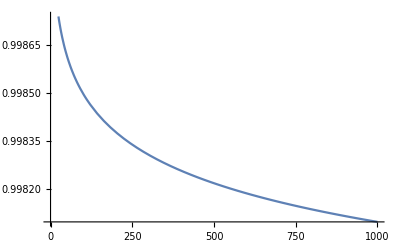

```mathematica
Plot[Evaluate[x/.soln],{t,0,tEnd}]
```

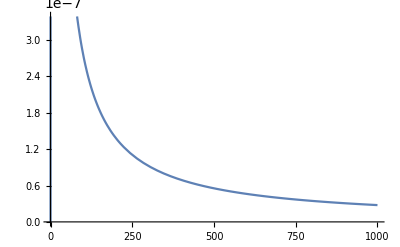

```mathematica
Plot[Evaluate[eH//.{g->gTest,V->VTest,W->WTest,r0->r0val,r1->r1val,r2->r2val,A->Aval,a->aval}/.soln],{t,0,tEnd}]
```

```mathematica
infEnd=FindRoot[Evaluate[eH//.{g->gEGNO,V->vEGNO,a->0.5,c->1000,m->1}/.soln]-1,{t,tEnd*0.8}]
```

InterpolatingFunction::dmval: Input value {4259.17} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {t} = {18484.6}.

{t→1679.51}

```mathematica
Ninf=NIntegrate[Evaluate[H//.{g->gEGNO,V->vEGNO,a->0.5,c->1000,m->1}/.soln],{t,0,t/.infEnd}]
```

{1066.36}

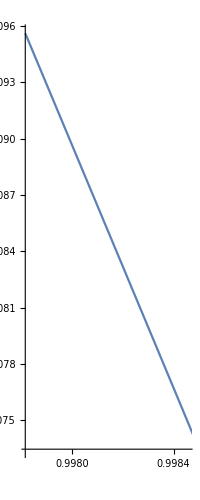

```mathematica
ParametricPlot[Evaluate[{x,y}/.soln],{t,0,tEnd},AspectRatio->Full]
```

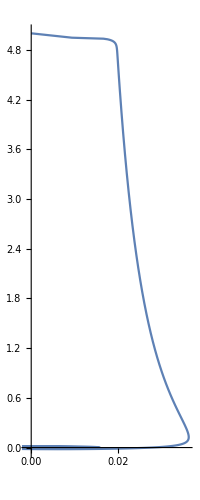

```mathematica
ParametricPlot[Evaluate[{-Sqrt[3/2]Log[x1/aVal],Sqrt[3/2] y1/aVal}/.soln],{t,0,tEnd},AspectRatio->Full]
```

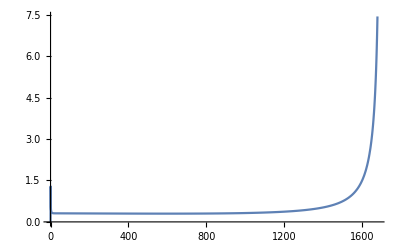

```mathematica
Plot[Evaluate[w/H//.{g->gEGNO,V->vEGNO,a->aVal,c->cVal,m->1}/.soln],{t,0,(*tEnd*)t/.infEnd},PlotRange->All]
```

```mathematica
Evaluate[w/H//.{g->gEGNO,V->vEGNO,a->aVal,c->cVal,m->1}/.soln/.t->500]
```

{0.29964028762721518479317973}

```mathematica
FindMinimum[Evaluate[w/H//.{g->gEGNO,V->vEGNO,a->aVal,c->cVal,m->1}/.soln],{t,t/.infEnd}]
```

InterpolatingFunction::dmval: Input value {-12278.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.299027,{t→597.704}}

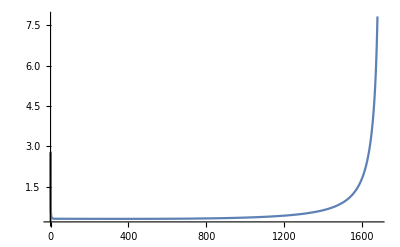

```mathematica
Plot[Evaluate[Sqrt[(sig.DdV.sig)/H^2]]//.{g->gEGNO,V->vEGNO,a->aVal,c->cVal,m->1}/.soln,{t,0,t/.infEnd},PlotRange->All]
```

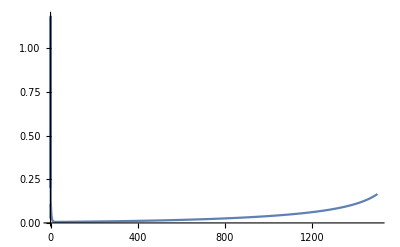

```mathematica
Plot[Evaluate[Sqrt[(sig.DdV.sig)/H^2]-w/H]//.{g->gEGNO,V->vEGNO,a->aVal,c->cVal,m->1}/.soln,{t,0,(*t/.infEnd*)1500},PlotRange->All]
```

```mathematica
Evaluate[Sqrt[(sig.DdV.sig)/H^2]]//.{g->gEGNO,V->vEGNO,a->aVal,c->cVal,m->1}/.soln/.t->500
```

{0.31392624864711102582265307}

#### Check axion inflation consistency

```mathematica
eomCheck=(-D[vEGNO[r,θ],θ]/(vEGNO[r,θ] gEGNO[r]^2)+√(D[vEGNO[r,θ],r]/(vEGNO[r,θ]/3 gEGNO[r] gEGNO'[r])))/((-D[vEGNO[r,θ],θ]/(vEGNO[r,θ] gEGNO[r]^2)-√(D[vEGNO[r,θ],r]/(vEGNO[r,θ] gEGNO[r]gEGNO'[r])))/2)(*√(D[vEGNO[r,θ],r]/(vEGNO[r,θ]/3 gEGNO[r] gEGNO'[r]))-(D[vEGNO[r,θ],θ]/(vEGNO[r,θ] gEGNO[r]^2))*);
```

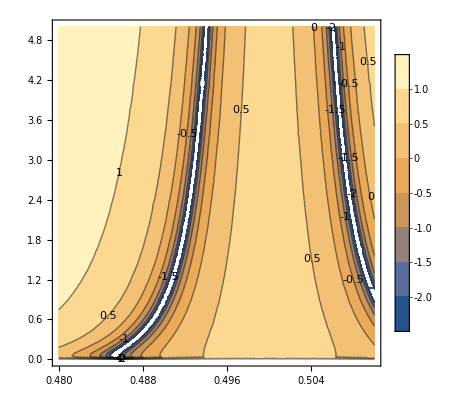

```mathematica
ContourPlot[Log@Abs@eomCheck//.{g->gEGNO,V->vEGNO,a->aVal,c->cVal,m->1},{r,0.48,0.51},{θ,0,5},PlotLegends->Automatic,ContourLabels->True(*,PlotPoints->50,MaxRecursion->1*)]
```